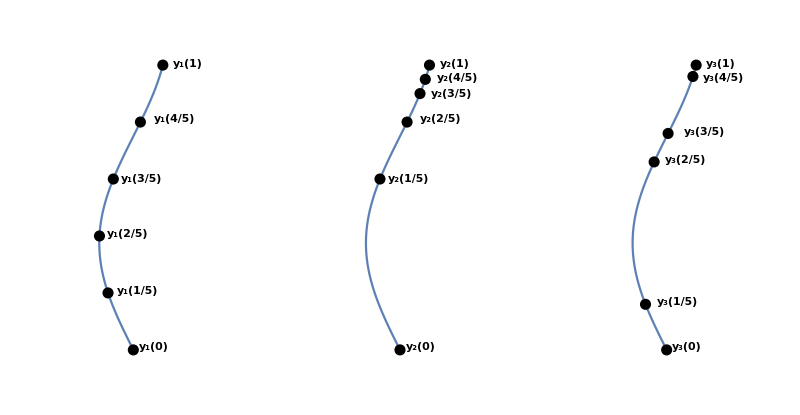

```mathematica
Y={-Sin[k]Cos[k]/2,k};
T=2/3 Pi;
curve= ParametricPlot[Y/.k->t,{t,0,T},Axes->False,PlotRange->{{-0.8,0.8},{-0.2,T+0.2}}];
ptsize=0.02;
p1 = Graphics[Join[{ PointSize->ptsize,Table[Point[Y/.k->i T/5],{i,0,5}]}]];
p2 = Graphics[{PointSize->ptsize,Point[Y/.k->0 T/5],Point[Y/.k->3 T/5],Point[Y/.k->4T/5],Point[Y/.k->4.5 T/5],Point[Y/.k->4.75 T/5],Point[Y/.k->T]}];
p3 = Graphics[{PointSize->ptsize,Point[Y/.k->0 T/5],Point[Y/.k->0.8 T/5],Point[Y/.k->3.3 T/5],Point[Y/.k->3.8 T/5],Point[Y/.k->4.8T/5],Point[Y/.k->T]}];
texts1=Graphics[{
Text[Style["y_1(0)",11,Bold],{0.15,0.02},FormatType->TraditionalForm],
Text[Style["y_1(1/5)",11,Bold],{0.03,0.43},FormatType->TraditionalForm],
Text[Style["y_1(2/5)",11,Bold],{-0.04,0.85},FormatType->TraditionalForm],Text[Style["y_1(3/5)",11,Bold],{0.06,1.26},FormatType->TraditionalForm],Text[Style["y_1(4/5)",11,Bold],{0.3,1.7},FormatType->TraditionalForm],
Text[Style["y_1(1)",11,Bold],{0.4,2.1},FormatType->TraditionalForm]
}];
texts2=Graphics[{
Text[Style["y_2(0)",11,Bold],{0.15,0.02},FormatType->TraditionalForm],
Text[Style["y_2(1/5)",11,Bold],{0.06,1.26},FormatType->TraditionalForm],
Text[Style["y_2(2/5)",11,Bold],{0.3,1.7},FormatType->TraditionalForm],Text[Style["y_2(3/5)",11,Bold],{0.38,1.88},FormatType->TraditionalForm],Text[Style["y_2(4/5)",11,Bold],{0.42,2.00},FormatType->TraditionalForm],
Text[Style["y_2(1)",11,Bold],{0.4,2.1},FormatType->TraditionalForm]
}];
texts3=Graphics[{
Text[Style["y_3(0)",11,Bold],{0.15,0.02},FormatType->TraditionalForm],
Text[Style["y_3(1/5)",11,Bold],{0.08,0.35},FormatType->TraditionalForm],
Text[Style["y_3(2/5)",11,Bold],{0.14,1.4},FormatType->TraditionalForm],Text[Style["y_3(3/5)",11,Bold],{0.28,1.6},FormatType->TraditionalForm],Text[Style["y_3(4/5)",11,Bold],{0.42,2.00},FormatType->TraditionalForm],
Text[Style["y_3(1)",11,Bold],{0.4,2.1},FormatType->TraditionalForm]
}];
Show[GraphicsRow[{Show[curve,texts1,p1],Show[curve,texts2,p2],Show[curve,texts3,p3]},Spacings->0],ImageSize->800]
```